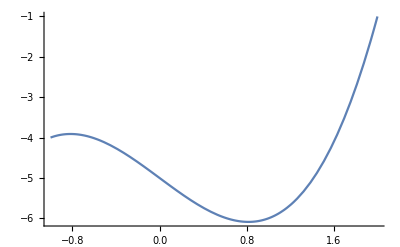

```mathematica
Plot[f[x],{x,-1,2}]
```

```mathematica
Res=1.*^-8;
```

```mathematica
f[x_]:=Cos[x]
```

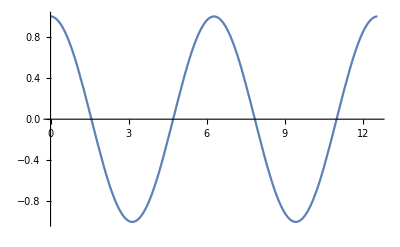

```mathematica
Plot[f[x],{x,0,4 Pi}]
```

```mathematica
(*FUNCIÓN PARA VER EL LÍMITE SUPERIOR Y EL INFERIOR*)
```

```mathematica
GoldenSearchLowUppIterMin[lower_,upper_,iterations_]:=Module[{a=N[lower],b=N[upper],n=iterations,c,d},k=0;
Print["Iteration Results are:"];
While[Abs[(b-(b-a)/GoldenRatio)-(a+(b-a)/GoldenRatio)]>Res,c=(b-(b-a)/GoldenRatio);
d=(a+(b-a)/GoldenRatio);
If[f[c]<f[d],(*Then*)b=d;(*Else*)k=k+1;,a=c;
Print[{"Lowerbound at iteration...",k,PaddedForm[a,{7,6}]}];
Print[{"Upperbound at iteration...",k,PaddedForm[b,{7,6}]}];
Print[(b+a)/2];
k++;]]];
```

```mathematica
(*FUNCIÓN PARA ÚNICAMENTE VER EL VALOR MÍNIMO Y PONER UNA FUNCIÓN*)
```

```mathematica
GoldenSearchMin[f_,lower_,upper_]:=Module[{a=N[lower],b=N[upper],c,d},k=0;
While[Abs[(b-(b-a)/GoldenRatio)-(a+(b-a)/GoldenRatio)]>Res,c=(b-(b-a)/GoldenRatio);
d=(a+(b-a)/GoldenRatio);
If[f[c]<f[d],(*Then*)b=d(*Else*); k=k+1;,a=c;k++;]];Print[(b+a)/2]];
```

```mathematica
GoldenSearchMin[f,2Pi,4 Pi]
```

9.42478

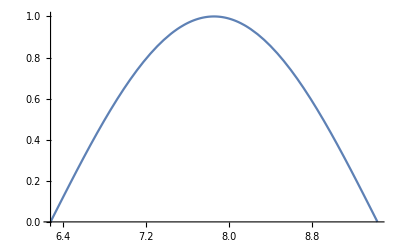

```mathematica
g[x_]:=Sin[x]
Plot[g[x],{x,2 Pi,3Pi}]
```

```mathematica
(*FUNCIÓN PARA VER EL VALOR MÁXIMO Y PONER UNA FUNCIÓN*)
```

```mathematica
GoldenSearchMax[f_,lower_,upper_]:=Module[{a=N[lower],b=N[upper],c,d},k=0;
While[Abs[(b-(b-a)/GoldenRatio)-(a+(b-a)/GoldenRatio)]>Res,c=(b-(b-a)/GoldenRatio);
d=(a+(b-a)/GoldenRatio);
If[f[c]>f[d],(*Then*)b=d(*Else*); k=k+1;,a=c;k++;]];Print[(b+a)/2]];
```

```mathematica
GoldenSearchMax[g,2 Pi,3 Pi]
```

7.85398